```mathematica
ClearAll[pdfSameN];
pdfSameN[a1_, a2_, s_] := pdfSameN[a1, a2, s] = (
in = Integrate[
1 * Boole[y < (2 - a1 - a2 -x) && y > a1 + a2 - x],
{x, -1, 1},
{y, -1, 1}
];
s/4(1 - 1/4 in)^(s - 1)
)
```

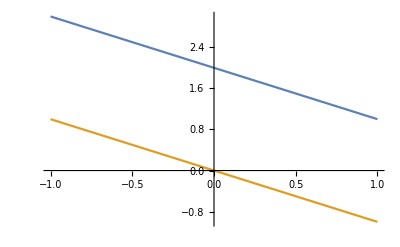

```mathematica
a1 = 0;
a2 = 0;
Plot[
{ 2 - (a1 + a2)- x, (a1 + a2) -x},
{x, -1, 1}
]
```

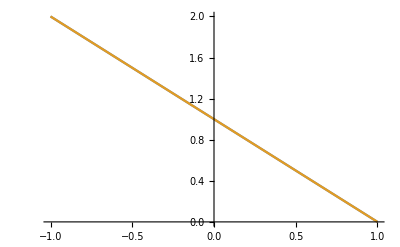

```mathematica
a1 = 0.5;
a2 = 0.5;
Plot[
{ 2 - (a1 + a2)- x, (a1 + a2) -x},
{x, -1, 1}
]
```

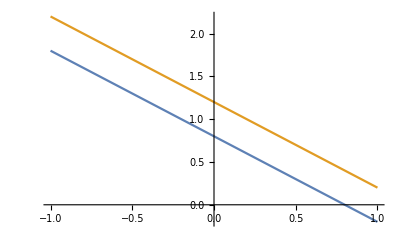

```mathematica
a1 = 0.6;
a2 = 0.6;
Plot[
{ 2 - (a1 + a2)- x, (a1 + a2) -x},
{x, -1, 1}
]
```

```mathematica
pdfSameN[0.1,0.1,2]
```

1.6

0.3

```mathematica
pdfSameN[0.2,0.2,2]
```

1.2

0.35

```mathematica
pdfSameN[0.3,0.3,2]
```

0.8

0.4

```mathematica
pdfSameN[0.5,0.5,2]
```

0.

0.5

```mathematica
pdfSameN[0.7,0.7,2]
```

0.

0.5

```mathematica
pdfSameN[0.63,0.63,2]
```

0.

0.5

```mathematica
ClearAll[pdfSameN];
pdfSameN[a1_, a2_, s_] := pdfSameN[a1, a2, s] = (
in = Integrate[
1 * Boole[y < 1 - x + Abs[1 - a1 - a2] && y >  1 - x - Abs[1 - a1 - a2]],
{x, -1, 1},
{y, -1, 1}
];
s/4(1 - 1/4 in)^(s - 1)
)
```

```mathematica
pdfSameN[0.7,0.7,2]
```

0.4

```mathematica
pdfSameN[0.6,0.6,2]
```

0.45

```mathematica
pdfSameN[0.5,0.5,2]
```

0.5

```mathematica
Integrate[pdfSameN[x0,y0,2], {x0,-1, 1}, {y0 ,-1, 1}]
```

1

```mathematica
Integrate[pdfSameN[x0,y0,10], {x0,-1, 1}, {y0 ,-1, 1}]
```

1

```mathematica
Integrate[pdfSameN[x0,y0,100], {x0,-1, 1}, {y0 ,-1, 1}]
```

1

```mathematica
Plot3D[pdfSameN[x0,y0,2], {x0,-1, 1}, {y0 ,-1, 1}]
```

-Graphics3D-

```mathematica
pdfSameN[x0,y0,s]
```

1/4 s (1-1/4 (Piecewise[{{2, Abs[1-x0-y0]==1}, {4, Abs[1-x0-y0]>3}, {2 Abs[1-x0-y0], 0<Abs[1-x0-y0]<1}, {1/2 (-1+6 Abs[1-x0-y0]-Abs[1-x0-y0]^2), 1<Abs[1-x0-y0]≤3}, {0, True}}]))^(-1+s)

```mathematica
Plot3D[Abs[1 - (x0 + y0)], {x0,-1, 1}, {y0 ,-1, 1}]
```

-Graphics3D-

Find the probability of going. We define

r = t / N

where t is the threshold, N is the attendance at the fixed point, and A is the total number  of agents.  Then

P_go = N/A = t/Ar

```mathematica
Integrate[
 pdfSameN[x0, y0, 2] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
```

Piecewise[{{1, r≥2}, {1/64 (2+r)^4, -2<r≤0}, {1/24 (6+12 r+3 r^2-2 r^3), 0<r≤1}, {1/24 (-4+36 r-15 r^2+2 r^3), 1<r<2}, {0, True}}]

```mathematica
Solve[1/64 (2+r)^4 == (.6)/r]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-3.38177-1.16904 ⅈ},{r→-3.38177+1.16904 ⅈ},{r→-0.973703-1.80847 ⅈ},{r→-0.973703+1.80847 ⅈ},{r→0.710955}}

```mathematica
Solve[1/24 (6+12 r+3 r^2-2 r^3)== (.6)/r]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-1.35252-0.841953 ⅈ},{r→-1.35252+0.841953 ⅈ},{r→0.843971},{r→3.36108}}

```mathematica
Solve[1/24 (-4+36 r-15 r^2+2 r^3)== (.6)/r]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-0.525993},{r→0.848576},{r→3.58871-1.80339 ⅈ},{r→3.58871+1.80339 ⅈ}}

```mathematica
60 / 0.84
```

71.4286

Whoa!  This is right!  The one fixed point at s=2 is in the third case.  What about for more general s?

```mathematica
Integrate[
 pdfSameN[x0, y0, s] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
```

∫_-1^1 ∫_-1^1 1/4 s Boole[y0<r-x0] (1-1/4 (Piecewise[{{2, Abs[1-x0-y0]==1}, {4, Abs[1-x0-y0]>3}, {2 Abs[1-x0-y0], 0<Abs[1-x0-y0]<1}, {1/2 (-1+6 Abs[1-x0-y0]-Abs[1-x0-y0]^2), 1<Abs[1-x0-y0]≤3}, {0, True}}]))^(-1+s)ⅆy0ⅆx0

```mathematica
Integrate[
 pdfSameN[x0, y0, 3] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
```

Piecewise[{{1, r≥2}, {1/512 (2+r)^6, -2<r≤0}, {1/64 (8+24 r+18 r^2-3 r^4), 0<r≤1}, {1/64 (-72+216 r-126 r^2+32 r^3-3 r^4), 1<r<2}, {0, True}}]

```mathematica
Solve[1/64 (8+24 r+18 r^2-3 r^4)== (.6)/r]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-2.05308},{r→-0.886784-1.25375 ⅈ},{r→-0.886784+1.25375 ⅈ},{r→0.904798},{r→2.92185}}

```mathematica
60 / 0.9047998
```

66.313

```mathematica
res = Integrate[
 pdfSameN[x0, y0, 100] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}, Assumptions-> 0 < r < 1]
```

(202+20200 r+994850 r^2+32330100 r^3+779838675 r^4+14891244060 r^5+234457885200 r^6+3130329602400 r^7+36175086462900 r^8+367544267675200 r^9+3323769638817320 r^10+27019819397006800 r^11+199072492910300100 r^12+1338398022348567600 r^13+8258895113516770800 r^14+47009015416315333920 r^15+247875860561504509950 r^16+1215391316301570500400 r^17+5559882205712886104900 r^18+23798888226361269452200 r^19+95570466898052138902910 r^20+360895469405231853199800 r^21+1284225436584851010087600 r^22+4314443183651930432493600 r^23+13708016309252308818165300 r^24+41253804196638398690637312 r^25+117761760777663698185413000 r^26+319265218108332692858230800 r^27+823023861435005179540275300 r^28+2019520735622029516182860400 r^29+4721500202592193144730963280 r^30+10526667594132180548201205600 r^31+22399073943196031905121315325 r^32+45521312550658375800382486200 r^33+88416395531086460689204444350 r^34+164226889125067525002918354060 r^35+291865814856625108210968843525 r^36+496545539926776144267878715300 r^37+809016989537447630935308112800 r^38+1262821679433561297726159422400 r^39+1889093128594507685493841973160 r^40+2709013948733822364152203593600 r^41+3724894179509005750709279941200 r^42+4911775290769048356265997047200 r^43+6212128577207291502181626486600 r^44+7536216076762272883397804150880 r^45+8769765511321826501140667234400 r^46+9788838099380500284415605652800 r^47+10479582723328721070614287503300 r^48+10758699938720042939323142618400 r^49+10589634653968727978848064662968 r^50+9990221371668611300800061002800 r^51+9029623162854321752646208983300 r^52+7815282030957012323847943222800 r^53+6473263904429040510661932770400 r^54+5126939837388144723743774690880 r^55+3878934745392346337042987430600 r^56+2799832598177934198166366867200 r^57+1924884911247329761239377221200 r^58+1257756476197846097642094525600 r^59+778841510260973929693758533160 r^60+455203163516748839878034210400 r^61+249627541283378396062147792800 r^62+127261099477800750933643972800 r^63+59369575426027582466811585525 r^64+24578173882663167007239481560 r^65+8378922914544261479740732350 r^66+1750819713486860607707018700 r^67-437704928371715151926754675 r^68-837348558624150725425095900 r^69-669878846899320580340076720 r^70-417831876335592313693005600 r^71-226325599681779169917044700 r^72-110658670445042713215499200 r^73-49721632328346894789396600 r^74-20726069896868810880632688 r^75-8057383632155937244265100 r^76-2929957684420340816096400 r^77-998117452934401816472400 r^78-318712882072152805423200 r^79-95379516914239846917090 r^80-26732997733720878014800 r^81-7009261600914620455100 r^82-1716473701092568864600 r^83-391803779597216806050 r^84-83158353220633771080 r^85-16363897771502173200 r^86-2975254140273122400 r^87-497818776605259900 r^88-76291254768019200 r^89-10648987644702680 r^90-1344877888538800 r^91-152447338297100 r^92-15359254587600 r^93-1358769442800 r^94-103921873440 r^95-6732743325 r^96-359297400 r^97-15165150 r^98-474700 r^99-9797 r^100-100 r^101)/256065421246102339102334047485952

```mathematica
fp = Solve[r == res, r, Assumptions->0 < r < 1]
```

{{r→Root7.89 × 10^-31Root[-202+«155»+10648987644702680 #1^90+1344877888538800 #1^91+152447338297100 #1^92+15359254587600 #1^93+1358769442800 #1^94+103921873440 #1^95+6732743325 #1^96+359297400 #1^97+15165150 #1^98+474700 #1^99+9797 #1^100+100 #1^101&,1]7.888609052210118e-31}}

```mathematica
N[fp]
```

{{r→7.88861×10^-31}}

```mathematica
pdfSameN[]
```

```mathematica
res2 = Integrate[
 pdfSameN[x0, y0, 2] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
```

Piecewise[{{1, r≥2}, {1/64 (2+r)^4, -2<r≤0}, {1/24 (6+12 r+3 r^2-2 r^3), 0<r≤1}, {1/24 (-4+36 r-15 r^2+2 r^3), 1<r<2}, {0, True}}]

```mathematica
TeXForm[res2]
```

\begin{cases}
 1 & r\geq 2 \\
 \frac{1}{64} (r+2)^4 & -2<r\leq 0 \\
 \frac{1}{24} \left(-2 r^3+3 r^2+12 r+6\right) & 0<r\leq 1 \\
 \frac{1}{24} \left(2 r^3-15 r^2+36 r-4\right) & 1<r<2
\end{cases}

```mathematica
Solve[0.6 / r == res2]
```

{{r→0.843971}}

```mathematica
60 / 0.843971
```

71.0925

```mathematica
res3 = Integrate[
 pdfSameN[x0, y0, 3] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
TeXForm[res3]
```

Piecewise[{{1, r≥2}, {1/512 (2+r)^6, -2<r≤0}, {1/64 (8+24 r+18 r^2-3 r^4), 0<r≤1}, {1/64 (-72+216 r-126 r^2+32 r^3-3 r^4), 1<r<2}, {0, True}}]

\begin{cases}
 1 & r\geq 2 \\
 \frac{1}{512} (r+2)^6 & -2<r\leq 0 \\
 \frac{1}{64} \left(-3 r^4+18 r^2+24 r+8\right) & 0<r\leq 1 \\
 \frac{1}{64} \left(-3 r^4+32 r^3-126 r^2+216 r-72\right) & 1<r<2
\end{cases}

```mathematica
Solve[0.6 / r == res3]
```

{{r→0.904798}}

```mathematica
60 / 0.904798
```

66.3131

```mathematica
Solve[0.8 / r == res3]
```

{{r→1.04424}}

```mathematica
80 / 1.0442353584023327
```

76.6111

```mathematica
Solve[0.2 / r == res3]
```

{{r→0.514231}}

```mathematica
20 / 0.514231
```

38.893

```mathematica
Solve[0.95 / r == res3]
```

{{r→1.1461}}

```mathematica
95 / 1.1461
```

82.8898

```mathematica
res5 = Integrate[
 pdfSameN[x0, y0, 5] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}, Assumptions->r > 0]
```

Piecewise[{{1, r≥2}, {1/384 (12+60 r+105 r^2+80 r^3+15 r^4-12 r^5-5 r^6), r≤1}, {1/384 (-1804+4860 r-4455 r^2+2160 r^3-585 r^4+84 r^5-5 r^6), True}}]

```mathematica
TeXForm[res5]
```

\begin{cases}
 1 & r\geq 2 \\
 \frac{1}{384} \left(-5 r^6-12 r^5+15 r^4+80 r^3+105 r^2+60 r+12\right) & r\leq 1 \\
 \frac{1}{384} \left(-5 r^6+84 r^5-585 r^4+2160 r^3-4455 r^2+4860 r-1804\right) &
   \text{True}
\end{cases}

```mathematica
Solve[0.6 / r == res5]
```

{{r→-2.31937},{r→0.965365}}

```mathematica
60 / 0.9653649307240628
```

62.1527

```mathematica
res10 = Integrate[
 pdfSameN[x0, y0, 10] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}, Assumptions->r > 0]
```

Piecewise[{{1, r≥2}, {(22+220 r+935 r^2+2310 r^3+3630 r^4+3696 r^5+2310 r^6+660 r^7-165 r^8-220 r^9-77 r^10-10 r^11)/22528, r≤1}, {1/22528(-1099404+4330260 r-7577955 r^2+7938810 r^3-5533110 r^4+2694384 r^5-935550 r^6+231660 r^7-40095 r^8+4620 r^9-319 r^10+10 r^11), True}}]

```mathematica
TeXForm[res10]
```

\begin{cases}
 1 & r\geq 2 \\
 \frac{-10 r^{11}-77 r^{10}-220 r^9-165 r^8+660 r^7+2310 r^6+3696 r^5+3630 r^4+2310
   r^3+935 r^2+220 r+22}{22528} & r\leq 1 \\
 \frac{10 r^{11}-319 r^{10}+4620 r^9-40095 r^8+231660 r^7-935550 r^6+2694384 r^5-5533110
   r^4+7938810 r^3-7577955 r^2+4330260 r-1099404}{22528} & \text{True}
\end{cases}

```mathematica
Solve[0.6 / r == res10]
```

{{r→1.00297}}

```mathematica
60 / 1.0029680120812179
```

59.8224

```mathematica
N[(8858 + 2936 + 8831) / 3]
```

6875.

```mathematica
N[(8865 + 2903 + 8849) / 3]
```

6872.33

```mathematica
res5/.r->0.965365
```

0.621527

```mathematica
res100 = Integrate[
 pdfSameN[x0, y0, 100] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}, Assumptions->r > 0]
```

Piecewise[{{1, r≥2}, {(202+20200 r+994850 r^2+32330100 r^3+779838675 r^4+14891244060 r^5+234457885200 r^6+3130329602400 r^7+36175086462900 r^8+367544267675200 r^9+3323769638817320 r^10+27019819397006800 r^11+199072492910300100 r^12+1338398022348567600 r^13+8258895113516770800 r^14+47009015416315333920 r^15+247875860561504509950 r^16+1215391316301570500400 r^17+5559882205712886104900 r^18+23798888226361269452200 r^19+95570466898052138902910 r^20+360895469405231853199800 r^21+1284225436584851010087600 r^22+4314443183651930432493600 r^23+13708016309252308818165300 r^24+41253804196638398690637312 r^25+117761760777663698185413000 r^26+319265218108332692858230800 r^27+823023861435005179540275300 r^28+2019520735622029516182860400 r^29+4721500202592193144730963280 r^30+10526667594132180548201205600 r^31+22399073943196031905121315325 r^32+45521312550658375800382486200 r^33+88416395531086460689204444350 r^34+164226889125067525002918354060 r^35+291865814856625108210968843525 r^36+496545539926776144267878715300 r^37+809016989537447630935308112800 r^38+1262821679433561297726159422400 r^39+1889093128594507685493841973160 r^40+2709013948733822364152203593600 r^41+3724894179509005750709279941200 r^42+4911775290769048356265997047200 r^43+6212128577207291502181626486600 r^44+7536216076762272883397804150880 r^45+8769765511321826501140667234400 r^46+9788838099380500284415605652800 r^47+10479582723328721070614287503300 r^48+10758699938720042939323142618400 r^49+10589634653968727978848064662968 r^50+9990221371668611300800061002800 r^51+9029623162854321752646208983300 r^52+7815282030957012323847943222800 r^53+6473263904429040510661932770400 r^54+5126939837388144723743774690880 r^55+3878934745392346337042987430600 r^56+2799832598177934198166366867200 r^57+1924884911247329761239377221200 r^58+1257756476197846097642094525600 r^59+778841510260973929693758533160 r^60+455203163516748839878034210400 r^61+249627541283378396062147792800 r^62+127261099477800750933643972800 r^63+59369575426027582466811585525 r^64+24578173882663167007239481560 r^65+8378922914544261479740732350 r^66+1750819713486860607707018700 r^67-437704928371715151926754675 r^68-837348558624150725425095900 r^69-669878846899320580340076720 r^70-417831876335592313693005600 r^71-226325599681779169917044700 r^72-110658670445042713215499200 r^73-49721632328346894789396600 r^74-20726069896868810880632688 r^75-8057383632155937244265100 r^76-2929957684420340816096400 r^77-998117452934401816472400 r^78-318712882072152805423200 r^79-95379516914239846917090 r^80-26732997733720878014800 r^81-7009261600914620455100 r^82-1716473701092568864600 r^83-391803779597216806050 r^84-83158353220633771080 r^85-16363897771502173200 r^86-2975254140273122400 r^87-497818776605259900 r^88-76291254768019200 r^89-10648987644702680 r^90-1344877888538800 r^91-152447338297100 r^92-15359254587600 r^93-1358769442800 r^94-103921873440 r^95-6732743325 r^96-359297400 r^97-15165150 r^98-474700 r^99-9797 r^100-100 r^101)/256065421246102339102334047485952, r≤1}, {(-102560126625670254620190343577256294165385349392248+3470208639595542962312171607088516569527523981473400 r-58125994713225344618728874418732652539586026689679450 r^2+642566966431774705188137109245890318124179857236157900 r^3-5273608593314243393157095565733391909555459603901041775 r^4+34270662346306157065284928425199461118648090194415045860 r^5-183672830875627769892376740579500379851577999734773448400 r^6+834954076709880477768597633714476755794513694496984061600 r^7-3286111736371532025975196755019475872623310571909853533700 r^8+11373509649019666400154626235300902000362376042766900475200 r^9-35046449283870215631758518149417587125475603613833647810440 r^10+97105646776099727522532301266546337533396953031805279057200 r^11-243920136544726696514932328181443776423175679639415641441300 r^12+559276356340491348869090189345908515439601254518956656059600 r^13-1177344566851546478347060479458637602583095902370094739575600 r^14+2286885878522909998316700261508702648397713042287576824352480 r^15-4116483634529653998138219220725848127810914539709627675455350 r^16+6892716783398490415487250788192117795404322019978911456576400 r^17-10771642792162867223379767435456612069155519699946467595205300 r^18+15757304930179878691877557763533991331498097942503952192387800 r^19-21633767732123108681096114856081300942740278505465288491659030 r^20+27941852648143349764233729559713617655985486915082368697641800 r^21-34022861902146998886477433788962586787728884893846851141481200 r^22+39129972590980003047481227214297714412957517428571452247314400 r^23-42581753206175311124117146281625027808995436571106846871232900 r^24+43913308179378879896488642096590043626281213152672699242751872 r^25-42978340766219027371219996557445612752370006004504530508874600 r^26+39971625568582305291751930954661351777924367724354007798377200 r^27-35368908886485754545451376747598050314242179152638991940430900 r^28+29808097600216157712010365820397080836004194127121544476000400 r^29-23951067896314035494913592185512040391034948965301170824575760 r^30+18365072017035648196081089373593070366042199211314650869386400 r^31-13449420947258443447945254310280794738174925781112223938314225 r^32+9414418230955142888395103896059073950269107171456752844660200 r^33-6303331746587782451138101171786678823025005663647768427602950 r^34+4039388314858093327976421425353425325460291796226025481625140 r^35-2479064291051322709596165570878111221822140145594557424026825 r^36+1457881779748027232708651710073614189869719372567395471902300 r^37-821927997146077797566340660808674547723160252865828669261600 r^38+444444025720663943766804135315563711946376170488305927617600 r^39-230594242756610585389933602139566634580581305822679174910280 r^40+114838239070543898020499640620582220303422468865667351113600 r^41-54912729396827538537580185296746656930803204358384586544400 r^42+25219336431789494523451056182796126207276147570813314248800 r^43-11127013763762870517578236471335105270640809662629691053800 r^44+4717406109630056490122789600467265480995957347594992933280 r^45-1922155257309467065944543636208448633857939380167596312800 r^46+752837187187641899036898983873217832279575041646188395200 r^47-283461562858761507716637269842507324044291212327147154900 r^48+102614194337920660371463831964799809062165405128976898400 r^49-35716359900198836303486927319360965799379507140053572056 r^50+11953266365528392337177686519197110374625002389576162000 r^51-3846499817625162149527691431177531671834455897158482900 r^52+1190122021299343562163119441533993863133926217597858800 r^53-354028067476465515846289498774956434300862237568792800 r^54+101242952917332502770942724550854711047639079940022720 r^55-27830423643614319870246488540062002263517210529069800 r^56+7352516463122049418764810181894605345160377601075200 r^57-1866519759450972854422424423869975692418138243376400 r^58+455212693428061571961625372252929506731008060674400 r^59-106627986199622174414267028410150025284666358398280 r^60+23981567037744422205120292905715536205551899498400 r^61-5177162114848051443785274150861666625019888973600 r^62+1072396409607277456518436037087808582668475451200 r^63-213055218623074326106179424194011589042397098825 r^64+40579572497030126107149470908201329857972796360 r^65-7406051454347784723412265696056027832205778950 r^66+1294477406176248489157386532061984776454253300 r^67-216557310431740818674825942393828280271482225 r^68+34652931181282740783443895032134059069659100 r^69-5300149815360373714710111024104654947967760 r^70+774250902395698343580355503285616383309600 r^71-107933124768124614768660669439507222158900 r^72+14345254143641290692264323923551078676800 r^73-1815963213334559254962713501451120253800 r^74+218713811188426037740564175559387670128 r^75-25032074369273373188709083353336244100 r^76+2718950226650708776105354980527667600 r^77-279877076470548617978886410110057200 r^78+27259120884593639862861577575343200 r^79-2507741066990943667239873548523030 r^80+217495132143114721350066469981200 r^81-17745682965219290563115179461300 r^82+1358907077815103243395948656600 r^83-97408992659998535430864607350 r^84+6516879603165979755563144520 r^85-405570627121367885213559600 r^86+23390441491573142805218400 r^87-1244739270941153949345300 r^88+60816451087756337500800 r^89-2712338636475552706440 r^90+109666530417595258800 r^91-3987126480699677700 r^92+129058966008680400 r^93-3673785780680400 r^94+90541298564640 r^95-1892692961775 r^96+32630736600 r^97-445455450 r^98+4514700 r^99-30199 r^100+100 r^101)/256065421246102339102334047485952, True}}]

```mathematica
TeXForm[res100]
```

\begin{cases}
 1 & r\geq 2 \\
 \frac{-100 r^{101}-9797 r^{100}-474700 r^{99}-15165150 r^{98}-359297400
   r^{97}-6732743325 r^{96}-103921873440 r^{95}-1358769442800 r^{94}-15359254587600
   r^{93}-152447338297100 r^{92}-1344877888538800 r^{91}-10648987644702680
   r^{90}-76291254768019200 r^{89}-497818776605259900 r^{88}-2975254140273122400
   r^{87}-16363897771502173200 r^{86}-83158353220633771080 r^{85}-391803779597216806050
   r^{84}-1716473701092568864600 r^{83}-7009261600914620455100
   r^{82}-26732997733720878014800 r^{81}-95379516914239846917090
   r^{80}-318712882072152805423200 r^{79}-998117452934401816472400
   r^{78}-2929957684420340816096400 r^{77}-8057383632155937244265100
   r^{76}-20726069896868810880632688 r^{75}-49721632328346894789396600
   r^{74}-110658670445042713215499200 r^{73}-226325599681779169917044700
   r^{72}-417831876335592313693005600 r^{71}-669878846899320580340076720
   r^{70}-837348558624150725425095900 r^{69}-437704928371715151926754675
   r^{68}+1750819713486860607707018700 r^{67}+8378922914544261479740732350
   r^{66}+24578173882663167007239481560 r^{65}+59369575426027582466811585525
   r^{64}+127261099477800750933643972800 r^{63}+249627541283378396062147792800
   r^{62}+455203163516748839878034210400 r^{61}+778841510260973929693758533160
   r^{60}+1257756476197846097642094525600 r^{59}+1924884911247329761239377221200
   r^{58}+2799832598177934198166366867200 r^{57}+3878934745392346337042987430600
   r^{56}+5126939837388144723743774690880 r^{55}+6473263904429040510661932770400
   r^{54}+7815282030957012323847943222800 r^{53}+9029623162854321752646208983300
   r^{52}+9990221371668611300800061002800 r^{51}+10589634653968727978848064662968
   r^{50}+10758699938720042939323142618400 r^{49}+10479582723328721070614287503300
   r^{48}+9788838099380500284415605652800 r^{47}+8769765511321826501140667234400
   r^{46}+7536216076762272883397804150880 r^{45}+6212128577207291502181626486600
   r^{44}+4911775290769048356265997047200 r^{43}+3724894179509005750709279941200
   r^{42}+2709013948733822364152203593600 r^{41}+1889093128594507685493841973160
   r^{40}+1262821679433561297726159422400 r^{39}+809016989537447630935308112800
   r^{38}+496545539926776144267878715300 r^{37}+291865814856625108210968843525
   r^{36}+164226889125067525002918354060 r^{35}+88416395531086460689204444350
   r^{34}+45521312550658375800382486200 r^{33}+22399073943196031905121315325
   r^{32}+10526667594132180548201205600 r^{31}+4721500202592193144730963280
   r^{30}+2019520735622029516182860400 r^{29}+823023861435005179540275300
   r^{28}+319265218108332692858230800 r^{27}+117761760777663698185413000
   r^{26}+41253804196638398690637312 r^{25}+13708016309252308818165300
   r^{24}+4314443183651930432493600 r^{23}+1284225436584851010087600
   r^{22}+360895469405231853199800 r^{21}+95570466898052138902910
   r^{20}+23798888226361269452200 r^{19}+5559882205712886104900
   r^{18}+1215391316301570500400 r^{17}+247875860561504509950 r^{16}+47009015416315333920
   r^{15}+8258895113516770800 r^{14}+1338398022348567600 r^{13}+199072492910300100
   r^{12}+27019819397006800 r^{11}+3323769638817320 r^{10}+367544267675200
   r^9+36175086462900 r^8+3130329602400 r^7+234457885200 r^6+14891244060 r^5+779838675
   r^4+32330100 r^3+994850 r^2+20200 r+202}{256065421246102339102334047485952} & r\leq 1
   \\
 \frac{100 r^{101}-30199 r^{100}+4514700 r^{99}-445455450 r^{98}+32630736600
   r^{97}-1892692961775 r^{96}+90541298564640 r^{95}-3673785780680400
   r^{94}+129058966008680400 r^{93}-3987126480699677700 r^{92}+109666530417595258800
   r^{91}-2712338636475552706440 r^{90}+60816451087756337500800
   r^{89}-1244739270941153949345300 r^{88}+23390441491573142805218400
   r^{87}-405570627121367885213559600 r^{86}+6516879603165979755563144520
   r^{85}-97408992659998535430864607350 r^{84}+1358907077815103243395948656600
   r^{83}-17745682965219290563115179461300 r^{82}+217495132143114721350066469981200
   r^{81}-2507741066990943667239873548523030 r^{80}+27259120884593639862861577575343200
   r^{79}-279877076470548617978886410110057200
   r^{78}+2718950226650708776105354980527667600
   r^{77}-25032074369273373188709083353336244100
   r^{76}+218713811188426037740564175559387670128
   r^{75}-1815963213334559254962713501451120253800
   r^{74}+14345254143641290692264323923551078676800
   r^{73}-107933124768124614768660669439507222158900
   r^{72}+774250902395698343580355503285616383309600
   r^{71}-5300149815360373714710111024104654947967760
   r^{70}+34652931181282740783443895032134059069659100
   r^{69}-216557310431740818674825942393828280271482225
   r^{68}+1294477406176248489157386532061984776454253300
   r^{67}-7406051454347784723412265696056027832205778950
   r^{66}+40579572497030126107149470908201329857972796360
   r^{65}-213055218623074326106179424194011589042397098825
   r^{64}+1072396409607277456518436037087808582668475451200
   r^{63}-5177162114848051443785274150861666625019888973600
   r^{62}+23981567037744422205120292905715536205551899498400
   r^{61}-106627986199622174414267028410150025284666358398280
   r^{60}+455212693428061571961625372252929506731008060674400
   r^{59}-1866519759450972854422424423869975692418138243376400
   r^{58}+7352516463122049418764810181894605345160377601075200
   r^{57}-27830423643614319870246488540062002263517210529069800
   r^{56}+101242952917332502770942724550854711047639079940022720
   r^{55}-354028067476465515846289498774956434300862237568792800
   r^{54}+1190122021299343562163119441533993863133926217597858800
   r^{53}-3846499817625162149527691431177531671834455897158482900
   r^{52}+11953266365528392337177686519197110374625002389576162000
   r^{51}-35716359900198836303486927319360965799379507140053572056
   r^{50}+102614194337920660371463831964799809062165405128976898400
   r^{49}-283461562858761507716637269842507324044291212327147154900
   r^{48}+752837187187641899036898983873217832279575041646188395200
   r^{47}-1922155257309467065944543636208448633857939380167596312800
   r^{46}+4717406109630056490122789600467265480995957347594992933280
   r^{45}-11127013763762870517578236471335105270640809662629691053800
   r^{44}+25219336431789494523451056182796126207276147570813314248800
   r^{43}-54912729396827538537580185296746656930803204358384586544400
   r^{42}+114838239070543898020499640620582220303422468865667351113600
   r^{41}-230594242756610585389933602139566634580581305822679174910280
   r^{40}+444444025720663943766804135315563711946376170488305927617600
   r^{39}-821927997146077797566340660808674547723160252865828669261600
   r^{38}+1457881779748027232708651710073614189869719372567395471902300
   r^{37}-2479064291051322709596165570878111221822140145594557424026825
   r^{36}+4039388314858093327976421425353425325460291796226025481625140
   r^{35}-6303331746587782451138101171786678823025005663647768427602950
   r^{34}+9414418230955142888395103896059073950269107171456752844660200
   r^{33}-13449420947258443447945254310280794738174925781112223938314225
   r^{32}+18365072017035648196081089373593070366042199211314650869386400
   r^{31}-23951067896314035494913592185512040391034948965301170824575760
   r^{30}+29808097600216157712010365820397080836004194127121544476000400
   r^{29}-35368908886485754545451376747598050314242179152638991940430900
   r^{28}+39971625568582305291751930954661351777924367724354007798377200
   r^{27}-42978340766219027371219996557445612752370006004504530508874600
   r^{26}+43913308179378879896488642096590043626281213152672699242751872
   r^{25}-42581753206175311124117146281625027808995436571106846871232900
   r^{24}+39129972590980003047481227214297714412957517428571452247314400
   r^{23}-34022861902146998886477433788962586787728884893846851141481200
   r^{22}+27941852648143349764233729559713617655985486915082368697641800
   r^{21}-21633767732123108681096114856081300942740278505465288491659030
   r^{20}+15757304930179878691877557763533991331498097942503952192387800
   r^{19}-10771642792162867223379767435456612069155519699946467595205300
   r^{18}+6892716783398490415487250788192117795404322019978911456576400
   r^{17}-4116483634529653998138219220725848127810914539709627675455350
   r^{16}+2286885878522909998316700261508702648397713042287576824352480
   r^{15}-1177344566851546478347060479458637602583095902370094739575600
   r^{14}+559276356340491348869090189345908515439601254518956656059600
   r^{13}-243920136544726696514932328181443776423175679639415641441300
   r^{12}+97105646776099727522532301266546337533396953031805279057200
   r^{11}-35046449283870215631758518149417587125475603613833647810440
   r^{10}+11373509649019666400154626235300902000362376042766900475200
   r^9-3286111736371532025975196755019475872623310571909853533700
   r^8+834954076709880477768597633714476755794513694496984061600
   r^7-183672830875627769892376740579500379851577999734773448400
   r^6+34270662346306157065284928425199461118648090194415045860
   r^5-5273608593314243393157095565733391909555459603901041775
   r^4+642566966431774705188137109245890318124179857236157900
   r^3-58125994713225344618728874418732652539586026689679450
   r^2+3470208639595542962312171607088516569527523981473400
   r-102560126625670254620190343577256294165385349392248}{2560654212461023391023340474859
   52} & \text{True}
\end{cases}

```mathematica
Solve[0.6 / r == res100]
```

{}

```mathematica
ClearAll[res];
ClearAll[t];
fixedPt[res_, t_ ] := fixedPt[res, t] = (
rRule = Solve[t / r == res];
100 t / (r/.rRule)
)

fixedPt[res2, 0.1]
```

{38.6347}

```mathematica
fixedPt[res2, 0.2]
```

{47.598}

```mathematica
fixedPt[res2, 0.3]
```

{54.7688}

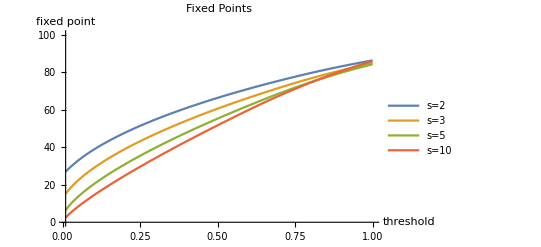

```mathematica
Plot[
{
fixedPt[res2, t],
fixedPt[res3, t],
fixedPt[res5, t],
fixedPt[res10, t],
}, 
{t,0.01,1},
PlotLegends->{"s=2", "s=3", "s=5", "s=10"},
PlotLabel->"Fixed Points",
PlotRange->{{0.01,1}, {0,100}},
AxesLabel->{"threshold", "fixed point"}
]
```

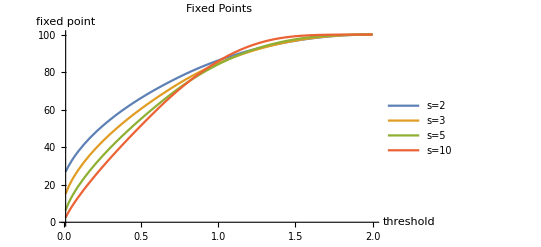

```mathematica
Plot[
{
fixedPt[res2, t],
fixedPt[res3, t],
fixedPt[res5, t],
fixedPt[res10, t],
}, 
{t,0.01,2},
PlotLegends->{"s=2", "s=3", "s=5", "s=10"},
PlotLabel->"Fixed Points",
PlotRange->{{0.01,2}, {0,100}},
AxesLabel->{"threshold", "fixed point"}
]
```

```mathematica
Plot[
{
fixedPt[res10, t],
}, 
{t,0,1}]
```

```mathematica
fixedPt[res10, 0.6]
```

{59.8224}

```mathematica
fixedPt[res10, 0.5]
```

{51.6277}

```mathematica
fixedPt[res10, 0.02]
```

{4.14197}

```mathematica
fixedPt[res10, 0]
```

{0,0}

```mathematica
fixedPt[res10, 0.001]
```

{0.527353}

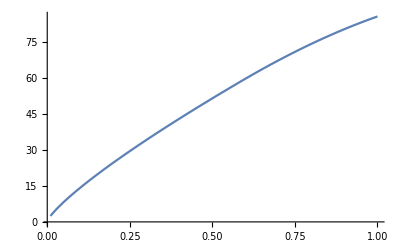

```mathematica
Plot[
{
fixedPt[res10, t],
}, 
{t,0.01,1}]
```

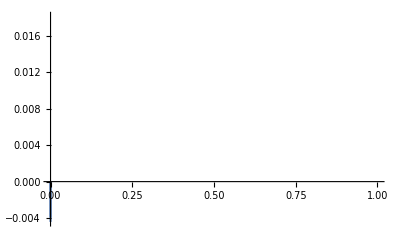

```mathematica
Plot[
{
fixedPt[res10, t],
}, 
{t,0,1}]
```

```mathematica
fixedPt[res20, 0.5]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{50./r}

```mathematica
rRule = N[Solve[0.5/ r == res20]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{res20→0.5/r}}

```mathematica
Integrate[
 pdfSameN[x0, y0, 3] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
```

Piecewise[{{71/64, r≥2}, {1/512 (2+r)^6, -2<r≤0}, {1/64 (-25+96 r-24 r^2), 1<r<2}, {1/64 (8+24 r+18 r^2-3 r^4), 0<r≤1}, {0, True}}]

```mathematica
pdfSameN[x0, y0, 3]
```

3/4 (1-1/4 (Piecewise[{{2, Abs[1-x0-y0]==1}, {4, Abs[1-x0-y0]>3}, {2 Abs[1-x0-y0], 0<Abs[1-x0-y0]<1}, {1/2 (-1+6 Abs[1-x0-y0]-Abs[1-x0-y0]^2), 1<Abs[1-x0-y0]≤3}, {0, True}}]))^2

```mathematica
pdfSameN[x0, y0, 2]
```

1/2 (1-1/4 (Piecewise[{{2, Abs[1-x0-y0]==1}, {4, Abs[1-x0-y0]>3}, {2 Abs[1-x0-y0], 0<Abs[1-x0-y0]<1}, {1/2 (-1+6 Abs[1-x0-y0]-Abs[1-x0-y0]^2), 1<Abs[1-x0-y0]≤3}, {0, True}}]))

```mathematica
pdfSameN[x0, y0, 4]
```

(1-1/4 (Piecewise[{{2, Abs[1-x0-y0]==1}, {4, Abs[1-x0-y0]>3}, {2 Abs[1-x0-y0], 0<Abs[1-x0-y0]<1}, {1/2 (-1+6 Abs[1-x0-y0]-Abs[1-x0-y0]^2), 1<Abs[1-x0-y0]≤3}, {0, True}}]))^3

```mathematica
pdfSameN[x0, y0, s]
```

1/4 s (1-1/4 (Piecewise[{{2, Abs[1-x0-y0]==1}, {4, Abs[1-x0-y0]>3}, {2 Abs[1-x0-y0], 0<Abs[1-x0-y0]<1}, {1/2 (-1+6 Abs[1-x0-y0]-Abs[1-x0-y0]^2), 1<Abs[1-x0-y0]≤3}, {0, True}}]))^(-1+s)

```mathematica
Integrate[
 pdfSameN[x0, y0, 2] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
```

Piecewise[{{1, r≥2}, {1/64 (2+r)^4, -2<r≤0}, {1/24 (6+12 r+3 r^2-2 r^3), 0<r≤1}, {1/24 (-4+36 r-15 r^2+2 r^3), 1<r<2}, {0, True}}]

```mathematica
Integrate[
 pdfSameN[x0, y0, 3] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
```

Piecewise[{{1, r≥2}, {1/512 (2+r)^6, -2<r≤0}, {1/64 (8+24 r+18 r^2-3 r^4), 0<r≤1}, {1/64 (-72+216 r-126 r^2+32 r^3-3 r^4), 1<r<2}, {0, True}}]

```mathematica
Integrate[
 pdfSameN[x0, y0, s] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
```

∫_-1^1 ∫_-1^1 1/4 s Boole[y0<r-x0] (1-1/4 (Piecewise[{{2, Abs[1-x0-y0]==1}, {4, Abs[1-x0-y0]>3}, {2 Abs[1-x0-y0], 0<Abs[1-x0-y0]<1}, {1/2 (-1+6 Abs[1-x0-y0]-Abs[1-x0-y0]^2), 1<Abs[1-x0-y0]≤3}, {0, True}}]))^(-1+s)ⅆy0ⅆx0

```mathematica
pgo2 = Integrate[
 pdfSameN[x0, y0, 2] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
sol2 = Solve[pgo2 == .6 / r, Assumptions->r > 0]
```

Piecewise[{{1, r≥2}, {1/64 (2+r)^4, -2<r≤0}, {1/24 (6+12 r+3 r^2-2 r^3), 0<r≤1}, {1/24 (-4+36 r-15 r^2+2 r^3), 1<r<2}, {0, True}}]

{{r→0.843971}}

```mathematica
Simplify[pgo2 , Assumptions->0  <=r ≤ 2]
```

```mathematica
Piecewise[{{1, r≥2}, {1/24 (6+12 r+3 r^2-2 r^3), r≤1}, {1/24 (-4+36 r-15 r^2+2 r^3), True}}]
```

```mathematica
pgo2 = Integrate[
 pdfSameN[x0+deltax, y0 + deltay, 2] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}, Assumptions->-{-1e-5<deltax<1e-5, -1e-5<deltay<1e-5}]
sol2 = Solve[pgo2 == .6 / r, Assumptions->r > 0]
```

Integrate[1/2 Boole[y0<r-x0] (1-1/4 (Piecewise[{{2, Abs[1-deltax-deltay-x0-y0]==1}, {4, Abs[1-deltax-deltay-x0-y0]>3}, {2 Abs[1-deltax-deltay-x0-y0], 0<Abs[1-deltax-deltay-x0-y0]<1}, {1/2 (-1+6 Abs[1-deltax-deltay-x0-y0]-Abs[1-deltax-deltay-x0-y0]^2), 1<Abs[1-deltax-deltay-x0-y0]≤3}, {0, True}}])),{x0,-1,1},{y0,-1,1},Assumptions→{-(-5-e<deltax<-5+e),-(-5-e<deltay<-5+e)}]

Solve::naqs: Integrate[1/2 Boole[y0<r-x0] (1-1/4 Piecewise[{{«2»},{«2»},{«2»},{«2»}},0]),{x0,-1,1},{y0,-1,1},Assumptions→{-(-5+Times[«2»]<deltax<-5+e),-(-5+Times[«2»]<deltay<-5+e)}]==0.6/r is not a quantified system of equations and inequalities.

Solve[Integrate[1/2 Boole[y0<r-x0] (1-1/4 (Piecewise[{{2, Abs[1-deltax-deltay-x0-y0]==1}, {4, Abs[1-deltax-deltay-x0-y0]>3}, {2 Abs[1-deltax-deltay-x0-y0], 0<Abs[1-deltax-deltay-x0-y0]<1}, {1/2 (-1+6 Abs[1-deltax-deltay-x0-y0]-Abs[1-deltax-deltay-x0-y0]^2), 1<Abs[1-deltax-deltay-x0-y0]≤3}, {0, True}}])),{x0,-1,1},{y0,-1,1},Assumptions→{-(-5-e<deltax<-5+e),-(-5-e<deltay<-5+e)}]==0.6/r,Assumptions→r>0]